```mathematica
output = Import["/home/john/Code/filter_testing/obj_dir/output_test.dat"];
input = Import["/home/john/Code/filter_testing/obj_dir/test.dat"];
```

```mathematica
twosComplement[n_]:=If[n[[1,1]]==1,-FromDigits[Flatten@BitXor[1, n],2]-1, FromDigits[Flatten@n,2]]
```

```mathematica
negatives = twosComplement/@IntegerDigits[output,2,39]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-8819,23336,37205,224979,416173,503453,466296,405003,410021,455716,454709,443070,407488,377868,14986,340119,364954,406869,433727,434784,445042,475050,491667,473714,455716,454709,443070,407488,377868,366335,340119,282471,232155,205711,169000,105304,47840,15528,-22433,-86508,-142591,-174524,-209854,-266680,-316996,-340119,-364954,-406869,-433727,-434784,-445042,-475050,-491667,-473714,-455716,-454709,-443070,-407488,-377868,-366335,-340119,-282471}
 |  |  |  |

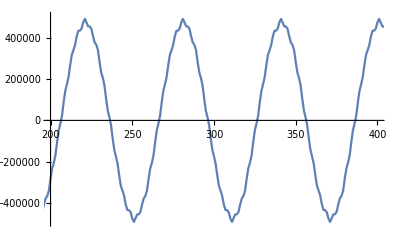

```mathematica
ListLinePlot[Interpolation@negatives,PlotRange->{{200,400},All}]
```

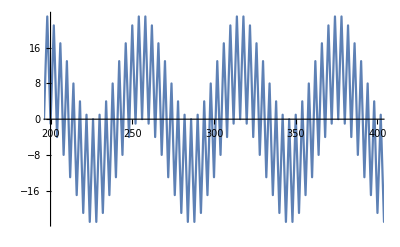

```mathematica
ListLinePlot[Interpolation@input,PlotRange->{{200,400},All}]
```

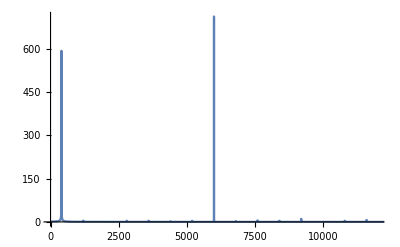

```mathematica
ListLinePlot[Abs@Fourier@Flatten@input,DataRange->{0,48000/2},PlotRange->{{0,48000/4},All}]
```

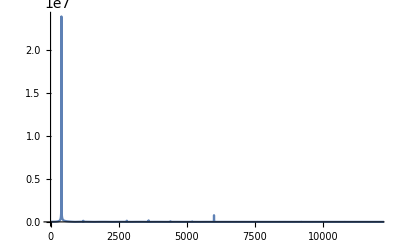

```mathematica
ListLinePlot[Abs@Fourier@Flatten@negatives,DataRange->{0,48000/2},PlotRange->{{0,48000/4},All}]
```